```mathematica
(*** SVD ***)

(*** Given a matrix A = {{1, 1}, {0, 1}}, which represents a 
horizontal shear, (1) find vectors w and v s.t. (w . v = 0) 
and (A(w).A(v) = 0) then (2) show how the image of a unit circle is
transformed by matrix A. ***)
```

```mathematica
(*** create a symmetric matrix ***)
A ={{1, 1}, {0, 1}}
```

```mathematica
{{1,1},{0,1}}//MatrixForm
```

(1 | 1
0 | 1)

```mathematica
S = Transpose[A].A
```

```mathematica
{{1,1},{1,2}}//MatrixForm
```

(1 | 1
1 | 2)

```mathematica
(*** solving this matrix's characteristic polynomial gives eigenvalues 
l = (3+√5)/2 and m = (3-√5)/2 with corresponding eigenvectors w and v. ***)
l = (3+√5)/2
```

1/2 (3+√5)

```mathematica
m = (3-√5)/2
```

1/2 (3-√5)

```mathematica
w = {1, (1+√5)/2}
```

{1,1/2 (1+√5)}

```mathematica
v = {1, (1-√5)/2}
```

{1,1/2 (1-√5)}

```mathematica
(*** find unit vectors ***)
```

```mathematica
√(w.w)
```

√(1+1/4 (1+√5)^2)

```mathematica
N[√(1+1/4 (1+√5)^2)]
```

1.90211

```mathematica
w = (1/1.902113032590307)*w
```

{0.525731,0.850651}

```mathematica
√(v.v)
```

√(1+1/4 (1-√5)^2)

```mathematica
N[√(1+1/4 (1-√5)^2)]
```

1.17557

```mathematica
v= (1/1.1755705045849463)*v
```

{0.850651,-0.525731}

```mathematica
(*** check that the two vectors w and v are unit vectors and orthogonal ***)
u.u
```

1.

```mathematica
v.v
```

1.

```mathematica
u.v
```

```mathematica
-1.1102230246251565*^-16 (*** basically 0 ***)
```

```mathematica
(*** check that transformation of both vectors is orthogonal ***)
(A.u).(A.v)
```

```mathematica
-1.1102230246251565*^-16 (*** same ***)
```

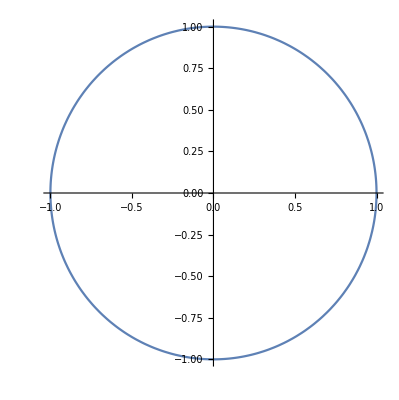

```mathematica
(*** Graph circle with initial vectors w and v ***)
ParametricPlot[Cos[t]*w+Sin[t]*v, {t, 0, 2π}]
```

```mathematica
(*** Now graph transformed vectors ***)
```

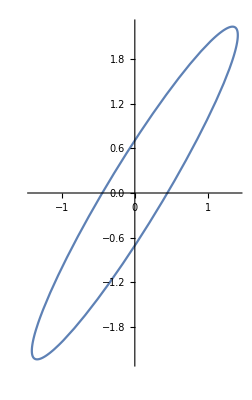

```mathematica
ParametricPlot[l*Cos[t]*(w)+m*Sin[t]*(v), {t, 0, 2π}]
```

```mathematica
(*** From just looking at this graph, it's clear that the vertical 
vector component is transformed more than the horizontal one, 
 suggesting its eigenvalue (and singular value) will be the greater
of the two. ***)
```

```mathematica
√l
```

√(1/2 (3+√5))

```mathematica
N[√(1/2 (3+√5))]
```

1.61803

```mathematica
√m
```

√(1/2 (3-√5))

```mathematica
N[√(1/2 (3-√5))]
```

0.618034

```mathematica
(*** From the above, if you could only include one value, the graph from 
including only l would look more like the full transformation than the graph
including only m. ***)
```

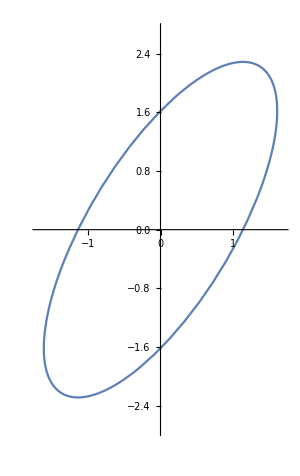

```mathematica
ParametricPlot[l*Cos[t]*(w)+Sin[t]*(v), {t, 0, 2π}, PlotRange->{{-1.7, 1.7},{-2.7, 2.7}}]
```

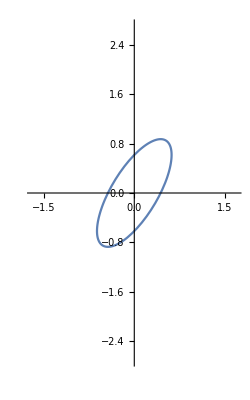

```mathematica
ParametricPlot[Cos[t]*(w)+m*Sin[t]*(v), {t, 0, 2π}, PlotRange->{{-1.7, 1.7},{-2.7, 2.7}}]
```

```mathematica
(*** This is basically the essence of lossy compression. Let's say you have
200 singular values instead of only 2. If that's the case, if you only include 
the 20 largest singular values you'll get a transformation that looks almost like the full transformation without having to include the full matrix X ***)
```